```mathematica
(* "dataIn" is the table of experimental data from the lab*)
dataIn = {{Diameter,Current,Voltage, B_field},{10.5 cm, 1.54 amp, 375 V, 0.00117 T},{5.5 cm, 2.88 amp, 373 V, 0.00220 T},{11cm, 1.59 amps, 440 V, 0.00121T},{5cm,3.39amp,440V,0.00266T},{8cm,2.18amp,442 V, 0.00166T}};

Grid[dataIn, Alignment->Left,Spacings->{2,1}]
```

Diameter | Current | Voltage | B_field
10.5 cm | 1.54 amp | 375 V | 0.00117 T
5.5 cm | 2.88 amp | 373 V | 0.0022 T
11 cm | 1.59 amps | 440 V | 0.00121 T
5 cm | 3.39 amp | 440 V | 0.00266 T
8 cm | 2.18 amp | 442 V | 0.00166 T

```mathematica
(* data set for lab 6; {x,y}= {tesla, diameter}*)
dataTD = {{0.00117, 0.105},{0.00121, 0.11},{0.00166,0.08},{0.00220, 0.055},{0.00266,0.05}};

(* data set for lab 6; {x,y}= {voltage, amps}, this data sets correspond to the {tesla,diameter} points in "dataTD"*)
```

```mathematica
dataVA ={{375,1.54},{440,1.59},{442,2.18},{373,2.88},{440,3.49}};
```

```mathematica
Needs["ErrorBarPlots`"]
```

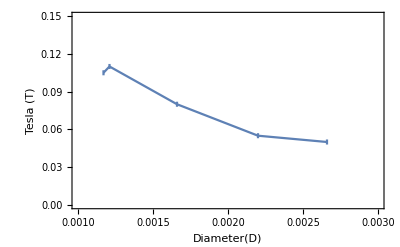

```mathematica
(*dataTD error list plot*)
ErrorListPlot[{{{0.00117, 0.105},ErrorBar[0.002]}, {{0.00121, 0.11},ErrorBar[0.002]}, {{0.00166,0.08},ErrorBar[0.002]}, {{0.00220, 0.055},ErrorBar[0.002]},{{0.00266,0.05},ErrorBar[0.002]}},Frame->True,FrameLabel->{"Diameter(D)", "Tesla (T)"},PlotRange-> {{0.0010,0.003}, {0.0,0.15}}, Joined -> True]
```

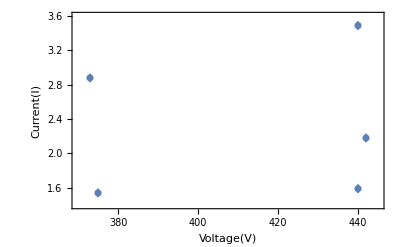

```mathematica
ErrorListPlot[{{{375,1.54},ErrorBar[0.05]}, {{440,1.59},ErrorBar[0.05]}, {{442,2.18},ErrorBar[0.05]}, {{373,2.88},ErrorBar[0.05]},{{440,3.49},ErrorBar[0.05]}},Frame->True,FrameLabel->{"Voltage(V)", "Current(I)"},PlotRange-> {{370,445}, {1.40,3.60}}]
```